# Chapter 1

## Section 1.1

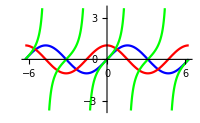

```mathematica
Plot[{Sin[x], Cos[x], Tan[x]}, {x,-2π,2π}, PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0], RGBColor[0,1,0]}, ImageSize->200]
```

## Section 1.2

```mathematica
π // Sin
```

0

```mathematica
Expand[(Sin[x]+Cos[x])^2, Trig -> False]
```

Cos[x]^2+2 Cos[x] Sin[x]+Sin[x]^2

```mathematica
Expand[(Sin[x]+Cos[x])^2,Trig->True]
```

1+2 Cos[x] Sin[x]

## Section 1.3

```mathematica
eq = {2x-3y+4z ==2, 3x-2y+z ==0, x+y-z==1} ;
sol = Solve[eq]
{{x->7/10,y->9/5,z->3/2}}
{2x-3y+4z ==2, 3x-2y+z ==0, x+y-z==1} /.sol
{{True,True,True}}
```

```mathematica
Roots[2 x^2+5x+1==0,x]
x==1/4 (-5-√17)||x==1/4 (-5+√17)
```

```mathematica
ToRules[Roots[2 x^2+5x+1==0,x]]
Sequence[{x->1/4 (-5-√17)},{x->1/4 (-5+√17)}]
```

## Section 1.4

```mathematica
Solve[{x==1+2a,y==9+2a x},{x,y}]
```

```mathematica
sol3 = Eliminate[{x==1+2a,y==9+2a x},y]
```

-1+x==2 a

```mathematica
Solve[sol3,x]
```

{{x→1+2 a}}

## Section 1.5

```mathematica
sol4 = NSolve[x^6+x^5-3x+6==0]
x^6+x^5-3x+6 /.sol4
Chop[%]
```

{{x→-1.46885-0.744043 ⅈ},{x→-1.46885+0.744043 ⅈ},{x→-0.0124087-1.34208 ⅈ},{x→-0.0124087+1.34208 ⅈ},{x→0.981254-0.5155 ⅈ},{x→0.981254+0.5155 ⅈ}}

{1.77636×10^-15+1.77636×10^-15 ⅈ,1.77636×10^-15-1.77636×10^-15 ⅈ,-1.24345×10^-14-1.24345×10^-14 ⅈ,-1.24345×10^-14+1.24345×10^-14 ⅈ,0.-2.22045×10^-16 ⅈ,0.+2.22045×10^-16 ⅈ}

{0,0,0,0,0,0}

## Section 1.6

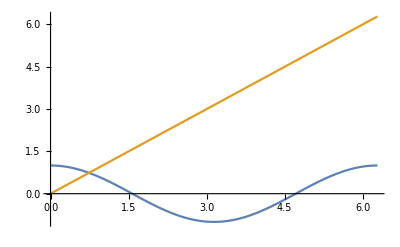

```mathematica
Plot[{Cos[x],x},{x,0,2π}]
```

```mathematica
sol161=FindRoot[Cos[x]==x,{x,0.5}]
```

{x→0.739085}

```mathematica
sol162=FindRoot[Cos[x]==x,{x,1.2}]
```

{x→0.739085}

```mathematica
Cos[x]-x /. sol162
```

0.

## Section 1.7

```mathematica
(* <<Algebra`IneualitySolve` is for Version 5.2 *)
Reduce[x^2-2x-3<0 &&x^2-2x-1 ≥0,x,Reals]
```

-1<x≤1-√2||1+√2≤x<3

```mathematica
Reduce[Sin[x]<1/2&&-π<x<π,x]
```

-π<x<π/6||(5 π)/6<x<π

## Section 1.8

```mathematica
Plot[{Sin[x],1/2},{x,-π,π},Ticks->{{π/6,(5π)/6},{-1,1/2,1}},GridLines->{{-π,-π/2,π/2,π},{-1,-0.5,0.5,1}},PlotLabel->"Plot of sin(x) and x=1/2",Frame->True,FrameLabel->{"정의역 x","치역 y"},LabelStyle->{FontFamily->"D2Coding"}]
```

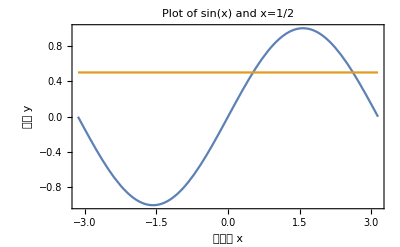

```mathematica
(* TextStyle Function is for Version 5.2 *)
?*Plot*
```

A Parametric function of x^2+y^2=4 is x=2sin(t), y=2cos(t) where t_1≤t≤t_2

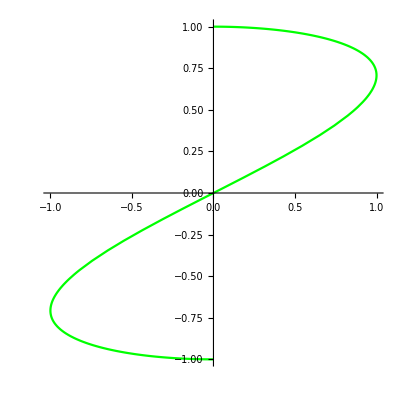

```mathematica
ParametricPlot[{Sin[t],Cos[1/2 t]},{t,0,2 π},PlotStyle->{RGBColor[0,1,0]}]
```

## Section 1.9

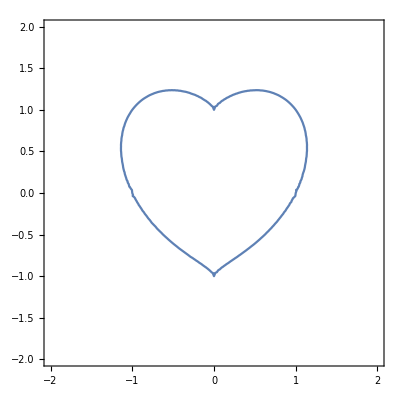

```mathematica
(* `ImplicitPlot` function is for version 5.2 *)
ContourPlot[(x^2+y^2-1)^3-x^2 y^3==0, {x,-2,2},{y,-2,2}]
```

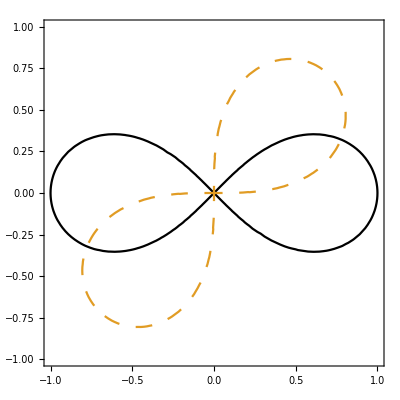

```mathematica
ContourPlot[{(x^2+y^2)^2==x^2-y^2,(x^2+y^2)^2==2 x y},{x,-1,1},{y,-1,1},ContourStyle->{GrayLevel[0],Dashing[{.03}]}]
```

```mathematica
gf = Plot3D[Sin[x^2+y^2],{x,-2,2},{y,-2,2},PlotPoints->5, FaceGrids->{{1,0,0},{-1,0,0},{0,1,0},{0,-1,0}},DisplayFunction->Identity];
```

```mathematica
gf2= ContourPlot[Cos[x^2+y^2],{x,-2,2},{y,-2,2}];
```

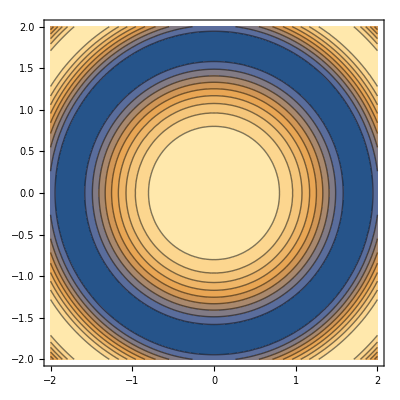

```mathematica
GraphicsGrid[{{gf,gf2}}]
```

```mathematica
gf3=ParametricPlot3D[{Sin[s]Sin[t],Sin[s]Cos[t],Cos[s]},{s,0,π},{t,0,2π},DisplayFunction->Identity]
```

-Graphics3D-

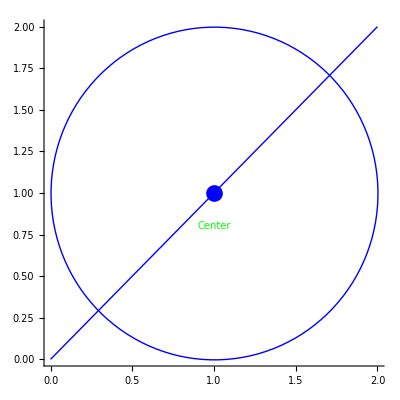

```mathematica
gf4=Show[Graphics[{RGBColor[0,0,1],PointSize[0.03],Point [{1,1}],Line[{{0,0},{2,2}}],Circle[{1,1},1],Text[Style["Center",{FontSize->10,FontColor->RGBColor[0,1,0]}],{1,0.8}]}],Axes->True]
```